```mathematica
(*High Resolution 13C Data- Michael's 75:25 samples*)
```

```mathematica
(*You need to evaluate customticks for this part to work*)
Needs["CustomTicks`"]
```

```mathematica
(*pre-set some plot options*)
SetOptions[LinTicks,TickReverse->True,MajorTickLength->{0.035,0.},MinorTickLength->{0.013,0.}];
SetOptions[LogTicks,TickReverse->True,MajorTickLength->{0.035,0.},MinorTickLength->{0.013,0.}];
SetOptions[ListPlot, Frame->{{False,False},{True,False}},FrameTicks->{{None,None},{LinTicks,None}}, FrameStyle->Black, AspectRatio->0.5, LabelStyle->Directive[FontSize->17, FontFamily->"Arial"]];
SetOptions[Plot, Frame->{{False,False},{True,False}}, FrameTicks->{{None,None},{LinTicks,None}},FrameStyle->Black, AspectRatio->0.4, LabelStyle->Directive[FontSize->17, FontFamily->"Arial"]];
```

```mathematica
(*Obviously you will need to set directory to where your files are stored on your own computer*)
SetDirectory["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\Michael 13C samples\\Michael High res samples"];
FileNames[]
```

{LK-MB-6040_1h_PLGAhr,LK-MB-6040-1hr.csv,LK-MB-6040-24h.csv,LK-MB_6040_24h_PLGAhr,LK-MB-6040-2h.csv,LK-MB_6040_2h_PLGAhr,LK-MB-6040-30min.csv,LK-MB_6040_30m_PLGAhr,Lk-MB_6040_48h_PLGAhr,LK-MB-6040-48hr.csv,LK-MB-6040-6h.csv,LK-MB_6040_6h_PLGAhr,LK-MB-7525-120h.csv,LK-MB-7525_120hr_hr,LK-MB-7525_1h,LK-MB-7525-1hr.csv,LK-MB-7525_24h,LK-MB-7525-24h.csv,LK-MB-7525_30min,LK-MB-7525-30min.csv,LK-MB-7525_48h,LK-MB-7525-48h.csv,LK-MB-7525_6h,LK-MB-7525-6h.csv,LK-MB-7525-72h.csv,LK-MB-7525_72hr_hr,MB_6040_highres.mnova,MB-7525-30mincomp.csv,MBhighres.mnova,output.csv}

```mathematica
(*The csv files referenced here are publicly posted at https://doi.org/10.18738/T8/QYLE8E*)
MBp5=Import["LK-MB-6040-30min.csv","TSV"];
MB1h=Import["LK-MB-6040-1hr.csv","TSV"];
MB2h = Import["LK-MB-6040-2h.csv", "TSV"];
MB6h=Import["LK-MB-6040-6h.csv","TSV"];
MB24h=Import["LK-MB-6040-24h.csv","TSV"];
MB48h=Import["LK-MB-6040-48hr.csv","TSV"];

(*set start and end of methylene resonance- different from 75:25 because sweep width was different*)
start=87430; end=87900;
MBp5[[start,1;;2]]
MBp5[[end,1;;2]]
```

{60.6948,12.0345}

{61.1191,9.81281}

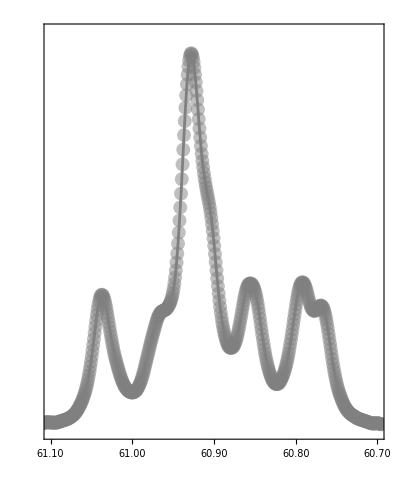

```mathematica
(*test plot to check resonance boundaries*)
a0p5=ListPlot[MBp5[[start;;end,1;;2]],PlotRange->{{60.7,61.1},{0,700.}},AspectRatio->1.2,PlotStyle->{Gray,PointSize[0.025],Opacity[0.5]},Axes->{True,False},ScalingFunctions->{"Reverse",None}];
b0p5=ListPlot[MBp5[[start;;end,1;;2]],PlotRange->{{60.7,61.1},{0,700.}},AspectRatio->1.2,PlotStyle->{Gray},Joined->True,ScalingFunctions->{"Reverse",None}];
dataplotMBp5=Show[{a0p5,b0p5}]
```

```mathematica
(*initial peak locations just for plotting dashed lines*)
ppm1=60.7656;
ppm2=60.7849;
ppm3=60.8227;
ppm4=60.8477;
ppm5=60.8738;
ppm6=60.9007;
ppm7=60.9225;
ppm8=60.9638;
ppm9 = 61.0256;
```

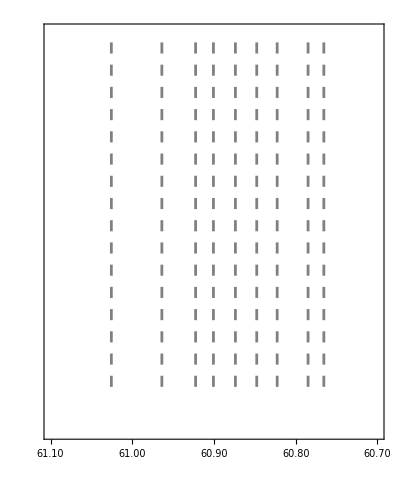

```mathematica
dashed=ListPlot[{{{ppm1,0},{ppm1,5000}},{{ppm2,0},{ppm2,5000}},{{ppm3,0},{ppm3,5000}},{{ppm4,0},{ppm4,5000}},{{ppm5,0},{ppm5,5000}},{{ppm6,0},{ppm6,5000}},{{ppm7,0},{ppm7,5000}},{{ppm8,0},{ppm8,5000}},{{ppm9,0},{ppm9,5000}}},Joined->True,ScalingFunctions->{"Reverse",None},Axes->{True,False},PlotStyle->{{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]},{Gray,Dashing[0.02]}},PlotRange->{{60.7,61.1},{-500,4000.}},AspectRatio->1.2]
```

```mathematica
(*Define Lorentzian here*)
Lorentzian[scale_,ppm_,ppmavg_,width_]:=scale (width/(2 Pi ((ppm-ppmavg)^2+(width/2)^2)))
```

```mathematica
(*Now we start with fits*)
```

FittedModel[…]

{scale1→6.36729,scale2→8.92353,scale3→9.89943,scale5→7.42369,scale6→28.0178,scale7→4.71764,scale8→9.24445,ppmavg1→60.7671,ppmavg2→60.7926,ppmavg3→60.8548,ppmavg5→60.9053,ppmavg6→60.9282,ppmavg7→60.9689,ppmavg8→61.0364,width1→0.0244251,width2→0.0262379,width3→0.0283673,width5→0.0243901,width6→0.0295386,width7→0.0265503,width8→0.0259765}

0.999202

General::munfl: Exp[-737.849] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4262.77] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4355.13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
scale1 | 6.36729 | 0.207845 | 30.6347 | 3.63542×10^-112
scale2 | 8.92353 | 0.230244 | 38.7569 | 1.74403×10^-145
scale3 | 9.89943 | 0.128505 | 77.0356 | 2.57262×10^-261
scale5 | 7.42369 | 0.365855 | 20.2913 | 1.76936×10^-65
scale6 | 28.0178 | 0.452489 | 61.9193 | 2.54486×10^-222
scale7 | 4.71764 | 0.166695 | 28.3011 | 5.82361×10^-102
scale8 | 9.24445 | 0.0868527 | 106.438 | 3.597×10^-321
ppmavg1 | 60.7671 | 0.000221941 | 273799. | 0.
ppmavg2 | 60.7926 | 0.000180836 | 336176. | 0.
ppmavg3 | 60.8548 | 0.000124327 | 489474. | 0.
ppmavg5 | 60.9053 | 0.000245597 | 247989. | 0.
ppmavg6 | 60.9282 | 0.0000985142 | 618471. | 0.
ppmavg7 | 60.9689 | 0.000264676 | 230353. | 0.
ppmavg8 | 61.0364 | 0.000109702 | 556386. | 0.
width1 | 0.0244251 | 0.000661821 | 36.9059 | 3.32348×10^-138
width2 | 0.0262379 | 0.000590095 | 44.4639 | 8.90945×10^-167
width3 | 0.0283673 | 0.000440982 | 64.3275 | 5.06193×10^-229
width5 | 0.0243901 | 0.000799493 | 30.5069 | 1.29653×10^-111
width6 | 0.0295386 | 0.00035539 | 83.1158 | 3.4472×10^-275
width7 | 0.0265503 | 0.000938973 | 28.2759 | 7.52992×10^-102
width8 | 0.0259765 | 0.000331356 | 78.3946 | 1.69566×10^-264

| DF | SS | MS
Model | 21 | 2.28169×10^7 | 1.08652×10^6
Error | 450 | 18217.1 | 40.4825
Uncorrected Total | 471 | 2.28351×10^7 | 
Corrected Total | 470 | 9.8895×10^6 |

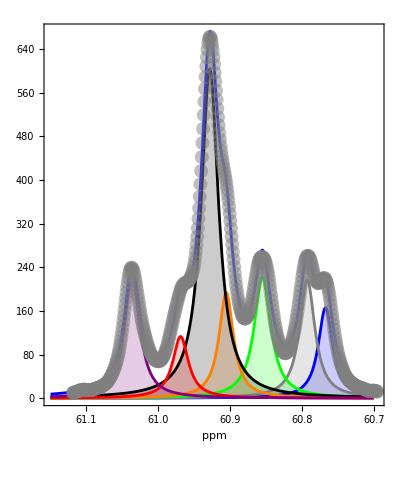

```mathematica
fit1=NonlinearModelFit[MBp5[[start;;end,1;;2]],{Lorentzian[scale1,x,ppmavg1,width1]+Lorentzian[scale2,x,ppmavg2,width2]+Lorentzian[scale3,x,ppmavg3,width3]+Lorentzian[scale5,x,ppmavg5,width5]+Lorentzian[scale6,x,ppmavg6,width6]+Lorentzian[scale7,x,ppmavg7,width7]+Lorentzian[scale8,x,ppmavg8,width8]},{{scale1,30.},{scale2,30.},{scale3,30.},{scale5,7.},{scale6,10},{scale7,25.},{scale8,16.},{ppmavg1,60.7587},{ppmavg2,60.7843},{ppmavg3,60.8474},{ppmavg5,60.8985},{ppmavg6,60.9198},{ppmavg7,60.9612},{ppmavg8,61.0303},{width1,0.02},{width2,0.01},{width3,0.01},{width5,0.024},{width6,0.02},{width7,0.015},{width8,0.01}},x]
fit1["BestFitParameters"]
fit1["RSquared"]
fit1["ParameterTable"]
fit1["ANOVATable"]
individualMBp5=Plot[{Lorentzian[fit1["BestFitParameters"][[1]][[2]],ppm,fit1["BestFitParameters"][[8]][[2]],fit1["BestFitParameters"][[15]][[2]]],Lorentzian[fit1["BestFitParameters"][[2]][[2]],ppm,fit1["BestFitParameters"][[9]][[2]],fit1["BestFitParameters"][[16]][[2]]],Lorentzian[fit1["BestFitParameters"][[3]][[2]],ppm,fit1["BestFitParameters"][[10]][[2]],fit1["BestFitParameters"][[17]][[2]]],Lorentzian[fit1["BestFitParameters"][[4]][[2]],ppm,fit1["BestFitParameters"][[11]][[2]],fit1["BestFitParameters"][[18]][[2]]],Lorentzian[fit1["BestFitParameters"][[5]][[2]],ppm,fit1["BestFitParameters"][[12]][[2]],fit1["BestFitParameters"][[19]][[2]]],Lorentzian[fit1["BestFitParameters"][[6]][[2]],ppm,fit1["BestFitParameters"][[13]][[2]],fit1["BestFitParameters"][[20]][[2]]],Lorentzian[fit1["BestFitParameters"][[7]][[2]],ppm,fit1["BestFitParameters"][[14]][[2]],fit1["BestFitParameters"][[21]][[2]]]},{ppm,60.7,61.15},PlotRange->{{60.7,61.101},{0,700.}},Filling->Axis,ScalingFunctions->{"Reverse",None},Axes->{{True,False},{False,False}},FrameLabel->{"ppm",None},AspectRatio->1.2,PlotStyle->{Blue,Gray,Green,Orange,Black,Red,Purple,Brown}];
cumulativeMBp5=Plot[Lorentzian[fit1["BestFitParameters"][[1]][[2]],ppm,fit1["BestFitParameters"][[8]][[2]],fit1["BestFitParameters"][[15]][[2]]]+Lorentzian[fit1["BestFitParameters"][[2]][[2]],ppm,fit1["BestFitParameters"][[9]][[2]],fit1["BestFitParameters"][[16]][[2]]]+Lorentzian[fit1["BestFitParameters"][[3]][[2]],ppm,fit1["BestFitParameters"][[10]][[2]],fit1["BestFitParameters"][[17]][[2]]]+Lorentzian[fit1["BestFitParameters"][[4]][[2]],ppm,fit1["BestFitParameters"][[11]][[2]],fit1["BestFitParameters"][[18]][[2]]]+Lorentzian[fit1["BestFitParameters"][[5]][[2]],ppm,fit1["BestFitParameters"][[12]][[2]],fit1["BestFitParameters"][[19]][[2]]]+Lorentzian[fit1["BestFitParameters"][[6]][[2]],ppm,fit1["BestFitParameters"][[13]][[2]],fit1["BestFitParameters"][[20]][[2]]]+Lorentzian[fit1["BestFitParameters"][[7]][[2]],ppm,fit1["BestFitParameters"][[14]][[2]],fit1["BestFitParameters"][[21]][[2]]],{ppm,60.7,61.15},PlotRange->{{60.7,61.1},{0,700.}},PlotStyle->{Blue},ScalingFunctions->{"Reverse",None},Axes->{True,False}];
Show[{individualMBp5,cumulativeMBp5,a0p5}]
```

FittedModel[…]

{scale1→7.12607,scale2→9.52075,scale3→11.2838,scale5→8.46266,scale6→27.4194,scale7→6.11482,scale8→10.3538,ppmavg1→60.7592,ppmavg2→60.7842,ppmavg3→60.8472,ppmavg5→60.8977,ppmavg6→60.9201,ppmavg7→60.9614,ppmavg8→61.0287,width1→0.0222953,width2→0.0250536,width3→0.027757,width5→0.0236166,width6→0.0280126,width7→0.0278531,width8→0.0258211}

0.999195

General::munfl: Exp[-753.04] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4377.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4408.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
scale1 | 7.12607 | 0.1953 | 36.4877 | 1.55604×10^-136
scale2 | 9.52075 | 0.218866 | 43.5004 | 2.66057×10^-163
scale3 | 11.2838 | 0.130248 | 86.6331 | 8.18059×10^-283
scale5 | 8.46266 | 0.361182 | 23.4305 | 5.97341×10^-80
scale6 | 27.4194 | 0.440077 | 62.306 | 2.07015×10^-223
scale7 | 6.11482 | 0.1756 | 34.8224 | 8.68411×10^-130
scale8 | 10.3538 | 0.0939251 | 110.235 | 0.
ppmavg1 | 60.7592 | 0.000171969 | 353314. | 0.
ppmavg2 | 60.7842 | 0.000160732 | 378172. | 0.
ppmavg3 | 60.8472 | 0.000112167 | 542468. | 0.
ppmavg5 | 60.8977 | 0.000213927 | 284667. | 0.
ppmavg6 | 60.9201 | 0.000094646 | 643663. | 0.
ppmavg7 | 60.9614 | 0.000233638 | 260922. | 0.
ppmavg8 | 61.0287 | 0.000104155 | 585941. | 0.
width1 | 0.0222953 | 0.000534508 | 41.7118 | 1.00756×10^-156
width2 | 0.0250536 | 0.000526209 | 47.6114 | 8.36223×10^-178
width3 | 0.027757 | 0.00039015 | 71.1444 | 6.02854×10^-247
width5 | 0.0236166 | 0.000690686 | 34.1929 | 3.37542×10^-127
width6 | 0.0280126 | 0.000339569 | 82.4946 | 8.19449×10^-274
width7 | 0.0278531 | 0.000825105 | 33.757 | 2.1569×10^-125
width8 | 0.0258211 | 0.000315775 | 81.7706 | 3.37903×10^-272

| DF | SS | MS
Model | 21 | 2.59507×10^7 | 1.23575×10^6
Error | 450 | 20916.6 | 46.4813
Uncorrected Total | 471 | 2.59717×10^7 | 
Corrected Total | 470 | 1.09426×10^7 |

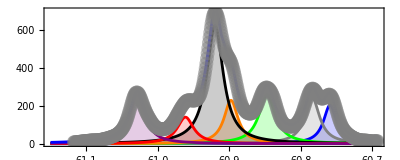

```mathematica
fit2=NonlinearModelFit[MB1h[[start;;end,1;;2]],{Lorentzian[scale1,x,ppmavg1,width1]+Lorentzian[scale2,x,ppmavg2,width2]+Lorentzian[scale3,x,ppmavg3,width3]+Lorentzian[scale5,x,ppmavg5,width5]+Lorentzian[scale6,x,ppmavg6,width6]+Lorentzian[scale7,x,ppmavg7,width7]+Lorentzian[scale8,x,ppmavg8,width8]},{{scale1,30.},{scale2,30.},{scale3,30.},{scale5,50.},{scale6,10},{scale7,25.},{scale8,16.},{ppmavg1,60.7587},{ppmavg2,60.7843},{ppmavg3,60.8474},{ppmavg5,60.8985},{ppmavg6,60.9198},{ppmavg7,60.9612},{ppmavg8,61.0303},{width1,0.02},{width2,0.01},{width3,0.01},{width5,0.02},{width6,0.02},{width7,0.015},{width8,0.01}},x]
fit2["BestFitParameters"]
fit2["RSquared"]
fit2["ParameterTable"]
fit2["ANOVATable"]
individualMB1h=Plot[{Lorentzian[fit2["BestFitParameters"][[1]][[2]],ppm,fit2["BestFitParameters"][[8]][[2]],fit2["BestFitParameters"][[15]][[2]]],Lorentzian[fit2["BestFitParameters"][[2]][[2]],ppm,fit2["BestFitParameters"][[9]][[2]],fit2["BestFitParameters"][[16]][[2]]],Lorentzian[fit2["BestFitParameters"][[3]][[2]],ppm,fit2["BestFitParameters"][[10]][[2]],fit2["BestFitParameters"][[17]][[2]]],Lorentzian[fit2["BestFitParameters"][[4]][[2]],ppm,fit2["BestFitParameters"][[11]][[2]],fit2["BestFitParameters"][[18]][[2]]],Lorentzian[fit2["BestFitParameters"][[5]][[2]],ppm,fit2["BestFitParameters"][[12]][[2]],fit2["BestFitParameters"][[19]][[2]]],Lorentzian[fit2["BestFitParameters"][[6]][[2]],ppm,fit2["BestFitParameters"][[13]][[2]],fit2["BestFitParameters"][[20]][[2]]],Lorentzian[fit2["BestFitParameters"][[7]][[2]],ppm,fit2["BestFitParameters"][[14]][[2]],fit2["BestFitParameters"][[21]][[2]]]},{ppm,60.7,61.15},PlotRange->{{60.7,61.101},{0,700.}},Filling->Axis,ScalingFunctions->{"Reverse",None},Axes->{True,False},PlotStyle->{Blue,Gray,Green,Orange,Black,Red,Purple,Brown}];
cumulativeMB1h=Plot[Lorentzian[fit2["BestFitParameters"][[1]][[2]],ppm,fit2["BestFitParameters"][[8]][[2]],fit2["BestFitParameters"][[15]][[2]]]+Lorentzian[fit2["BestFitParameters"][[2]][[2]],ppm,fit2["BestFitParameters"][[9]][[2]],fit2["BestFitParameters"][[16]][[2]]]+Lorentzian[fit2["BestFitParameters"][[3]][[2]],ppm,fit2["BestFitParameters"][[10]][[2]],fit2["BestFitParameters"][[17]][[2]]]+Lorentzian[fit2["BestFitParameters"][[4]][[2]],ppm,fit2["BestFitParameters"][[11]][[2]],fit2["BestFitParameters"][[18]][[2]]]+Lorentzian[fit2["BestFitParameters"][[5]][[2]],ppm,fit2["BestFitParameters"][[12]][[2]],fit2["BestFitParameters"][[19]][[2]]]+Lorentzian[fit2["BestFitParameters"][[6]][[2]],ppm,fit2["BestFitParameters"][[13]][[2]],fit2["BestFitParameters"][[20]][[2]]]+Lorentzian[fit2["BestFitParameters"][[7]][[2]],ppm,fit2["BestFitParameters"][[14]][[2]],fit2["BestFitParameters"][[21]][[2]]],{ppm,60.7,61.15},PlotRange->{{60.7,61.1},{0,700.}},PlotStyle->{Blue},ScalingFunctions->{"Reverse",None},Axes->{True,False}];
Show[{individualMB1h,cumulativeMB1h,ListPlot[MB1h[[start;;end,1;;2]],PlotRange->{{60.5,61.1},{-500,4500.}},Axes->{True,False},AspectRatio->1.2,PlotStyle->{Gray,PointSize[0.025],Opacity[0.5]},ScalingFunctions->{"Reverse",None}]}]
```

FittedModel[…]

{scale1→5.119,scale2→7.94347,scale3→11.1065,scale5→9.29048,scale6→21.9408,scale7→4.97275,scale8→9.43892,ppmavg1→60.771,ppmavg2→60.7954,ppmavg3→60.8586,ppmavg5→60.9101,ppmavg6→60.9319,ppmavg7→60.9729,ppmavg8→61.0395,width1→0.0225835,width2→0.0264968,width3→0.0312749,width5→0.0295582,width6→0.028052,width7→0.0322029,width8→0.0279514}

0.999395

General::munfl: Exp[-793.631] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4324.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4379.91] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
scale1 | 5.119 | 0.165009 | 31.0226 | 7.76766×10^-114
scale2 | 7.94347 | 0.190896 | 41.6114 | 2.38465×10^-156
scale3 | 11.1065 | 0.129051 | 86.0633 | 1.34645×10^-281
scale5 | 9.29048 | 0.426074 | 21.8048 | 1.82865×10^-72
scale6 | 21.9408 | 0.452226 | 48.5174 | 6.88379×10^-181
scale7 | 4.97275 | 0.161623 | 30.7676 | 9.71402×10^-113
scale8 | 9.43892 | 0.0780024 | 121.008 | 0.
ppmavg1 | 60.771 | 0.000193706 | 313728. | 0.
ppmavg2 | 60.7954 | 0.000171154 | 355209. | 0.
ppmavg3 | 60.8586 | 0.000107736 | 564884. | 0.
ppmavg5 | 60.9101 | 0.000290662 | 209556. | 0.
ppmavg6 | 60.9319 | 0.000105223 | 579076. | 0.
ppmavg7 | 60.9729 | 0.00029044 | 209933. | 0.
ppmavg8 | 61.0395 | 0.0000967653 | 630799. | 0.
width1 | 0.0225835 | 0.00059196 | 38.1504 | 4.04225×10^-143
width2 | 0.0264968 | 0.00055138 | 48.0554 | 2.54584×10^-179
width3 | 0.0312749 | 0.000400298 | 78.129 | 7.03613×10^-264
width5 | 0.0295582 | 0.000819672 | 36.061 | 8.0612×10^-135
width6 | 0.028052 | 0.000369526 | 75.9136 | 1.18416×10^-258
width7 | 0.0322029 | 0.00103086 | 31.2388 | 9.16485×10^-115
width8 | 0.0279514 | 0.000301223 | 92.7931 | 1.58127×10^-295

| DF | SS | MS
Model | 21 | 1.91414×10^7 | 911496.
Error | 450 | 11578.3 | 25.7296
Uncorrected Total | 471 | 1.9153×10^7 | 
Corrected Total | 470 | 7.85233×10^6 |

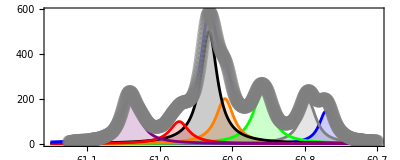

```mathematica
fit3=NonlinearModelFit[MB2h[[start;;end,1;;2]],{Lorentzian[scale1,x,ppmavg1,width1]+Lorentzian[scale2,x,ppmavg2,width2]+Lorentzian[scale3,x,ppmavg3,width3]+Lorentzian[scale5,x,ppmavg5,width5]+Lorentzian[scale6,x,ppmavg6,width6]+Lorentzian[scale7,x,ppmavg7,width7]+Lorentzian[scale8,x,ppmavg8,width8]},{{scale1,3.},{scale2,3.},{scale3,3.},{scale5,5.},{scale6,11},{scale7,2.},{scale8,1.},{ppmavg1,60.7587},{ppmavg2,60.7843},{ppmavg3,60.8474},{ppmavg5,60.91},{ppmavg6,60.93},{ppmavg7,60.97},{ppmavg8,61.0303},{width1,0.02},{width2,0.01},{width3,0.01},{width5,0.02},{width6,0.02},{width7,0.015},{width8,0.01}},x]
fit3["BestFitParameters"]
fit3["RSquared"]
fit3["ParameterTable"]
fit3["ANOVATable"]
individualMB2h=Plot[{Lorentzian[fit3["BestFitParameters"][[1]][[2]],ppm,fit3["BestFitParameters"][[8]][[2]],fit3["BestFitParameters"][[15]][[2]]],Lorentzian[fit3["BestFitParameters"][[2]][[2]],ppm,fit3["BestFitParameters"][[9]][[2]],fit3["BestFitParameters"][[16]][[2]]],Lorentzian[fit3["BestFitParameters"][[3]][[2]],ppm,fit3["BestFitParameters"][[10]][[2]],fit3["BestFitParameters"][[17]][[2]]],Lorentzian[fit3["BestFitParameters"][[4]][[2]],ppm,fit3["BestFitParameters"][[11]][[2]],fit3["BestFitParameters"][[18]][[2]]],Lorentzian[fit3["BestFitParameters"][[5]][[2]],ppm,fit3["BestFitParameters"][[12]][[2]],fit3["BestFitParameters"][[19]][[2]]],Lorentzian[fit3["BestFitParameters"][[6]][[2]],ppm,fit3["BestFitParameters"][[13]][[2]],fit3["BestFitParameters"][[20]][[2]]],Lorentzian[fit3["BestFitParameters"][[7]][[2]],ppm,fit3["BestFitParameters"][[14]][[2]],fit3["BestFitParameters"][[21]][[2]]]},{ppm,60.7,61.15},PlotRange->{{60.7,61.101},{0,700.}},Filling->Axis,ScalingFunctions->{"Reverse",None},Axes->{True,False},PlotStyle->{Blue,Gray,Green,Orange,Black,Red,Purple,Brown}];
cumulativeMB2h=Plot[Lorentzian[fit3["BestFitParameters"][[1]][[2]],ppm,fit3["BestFitParameters"][[8]][[2]],fit3["BestFitParameters"][[15]][[2]]]+Lorentzian[fit3["BestFitParameters"][[2]][[2]],ppm,fit3["BestFitParameters"][[9]][[2]],fit3["BestFitParameters"][[16]][[2]]]+Lorentzian[fit3["BestFitParameters"][[3]][[2]],ppm,fit3["BestFitParameters"][[10]][[2]],fit3["BestFitParameters"][[17]][[2]]]+Lorentzian[fit3["BestFitParameters"][[4]][[2]],ppm,fit3["BestFitParameters"][[11]][[2]],fit3["BestFitParameters"][[18]][[2]]]+Lorentzian[fit3["BestFitParameters"][[5]][[2]],ppm,fit3["BestFitParameters"][[12]][[2]],fit3["BestFitParameters"][[19]][[2]]]+Lorentzian[fit3["BestFitParameters"][[6]][[2]],ppm,fit3["BestFitParameters"][[13]][[2]],fit3["BestFitParameters"][[20]][[2]]]+Lorentzian[fit3["BestFitParameters"][[7]][[2]],ppm,fit3["BestFitParameters"][[14]][[2]],fit3["BestFitParameters"][[21]][[2]]],{ppm,60.7,61.15},PlotRange->{{60.7,61.1},{0,700.}},PlotStyle->{Blue},ScalingFunctions->{"Reverse",None},Axes->{True,False}];
Show[{individualMB2h,cumulativeMB2h,ListPlot[MB2h[[start;;end,1;;2]],PlotRange->{{60.5,61.1},{-500,4500.}},Axes->{True,False},AspectRatio->1.2,PlotStyle->{Gray,PointSize[0.025],Opacity[0.5]},ScalingFunctions->{"Reverse",None}]}]
```

FittedModel[…]

{scale1→4.09133,scale2→8.38226,scale3→15.2809,scale4→2.9131,scale5→9.99047,scale6→20.5148,scale7→7.23779,scale8→11.8397,ppmavg1→60.7626,ppmavg2→60.7845,ppmavg3→60.8467,ppmavg4→60.8732,ppmavg5→60.9004,ppmavg6→60.9211,ppmavg7→60.9628,ppmavg8→61.0263,width1→0.0198021,width2→0.0286393,width3→0.0356875,width4→0.0282097,width5→0.0286032,width6→0.028962,width7→0.0432084,width8→0.0300264}

0.998981

General::munfl: Exp[-4098.47] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4064.56] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4037.97] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
scale1 | 4.09133 | 0.28335 | 14.4392 | 4.6193×10^-39
scale2 | 8.38226 | 0.379621 | 22.0806 | 1.35102×10^-73
scale3 | 15.2809 | 0.642731 | 23.7749 | 2.31421×10^-81
scale4 | 2.9131 | 1.00434 | 2.90051 | 0.00390933
scale5 | 9.99047 | 1.39273 | 7.17332 | 3.05938×10^-12
scale6 | 20.5148 | 1.07829 | 19.0252 | 1.48609×10^-59
scale7 | 7.23779 | 0.394875 | 18.3293 | 2.2462×10^-56
scale8 | 11.8397 | 0.149501 | 79.1951 | 3.42483×10^-265
ppmavg1 | 60.7626 | 0.000301781 | 201347. | 0.
ppmavg2 | 60.7845 | 0.000325679 | 186639. | 0.
ppmavg3 | 60.8467 | 0.000346 | 175857. | 0.
ppmavg4 | 60.8732 | 0.00103779 | 58656.8 | 0.
ppmavg5 | 60.9004 | 0.000437394 | 139235. | 0.
ppmavg6 | 60.9211 | 0.000246431 | 247214. | 0.
ppmavg7 | 60.9628 | 0.000572412 | 106501. | 0.
ppmavg8 | 61.0263 | 0.000129047 | 472901. | 0.
width1 | 0.0198021 | 0.000980729 | 20.1912 | 6.62612×10^-65
width2 | 0.0286393 | 0.00103531 | 27.6625 | 6.91593×10^-99
width3 | 0.0356875 | 0.000931138 | 38.3267 | 2.31936×10^-143
width4 | 0.0282097 | 0.00617458 | 4.56869 | 6.35723×10^-6
width5 | 0.0286032 | 0.00236602 | 12.0892 | 2.62793×10^-29
width6 | 0.028962 | 0.000798402 | 36.2749 | 2.84036×10^-135
width7 | 0.0432084 | 0.00208422 | 20.7312 | 2.17535×10^-67
width8 | 0.0300264 | 0.000432697 | 69.3935 | 1.7944×10^-241

| DF | SS | MS
Model | 24 | 2.34877×10^7 | 978654.
Error | 447 | 23969.5 | 53.623
Uncorrected Total | 471 | 2.35117×10^7 | 
Corrected Total | 470 | 8.80402×10^6 |

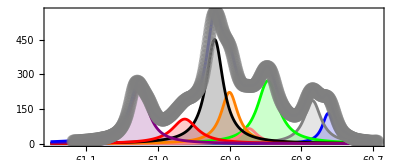

```mathematica
fit4=NonlinearModelFit[MB6h[[start;;end,1;;2]],{Lorentzian[scale1,x,ppmavg1,width1]+Lorentzian[scale2,x,ppmavg2,width2]+Lorentzian[scale3,x,ppmavg3,width3]+Lorentzian[scale4,x,ppmavg4,width4]+Lorentzian[scale5,x,ppmavg5,width5]+Lorentzian[scale6,x,ppmavg6,width6]+Lorentzian[scale7,x,ppmavg7,width7]+Lorentzian[scale8,x,ppmavg8,width8]},{{scale1, 5.1},{scale2,5.1},{scale3,15.1},{scale4,2.5},{scale5,10.},{scale6,20},{scale7,7.},{scale8,11.},{ppmavg1,60.7587},{ppmavg2,60.7843},{ppmavg3,60.84},{ppmavg4,60.87},{ppmavg5,60.8985},{ppmavg6,60.9198},{ppmavg7,60.9612},{ppmavg8,61.0303},{width1,0.02},{width2,0.01},{width3,0.01},{width4,0.05},{width5,0.02},{width6,0.02},{width7,0.015},{width8,0.01}},x]
fit4["BestFitParameters"]
fit4["RSquared"]
fit4["ParameterTable"]
fit4["ANOVATable"]
individualMB6h=Plot[{Lorentzian[fit4["BestFitParameters"][[1]][[2]],ppm,fit4["BestFitParameters"][[9]][[2]],fit4["BestFitParameters"][[17]][[2]]],Lorentzian[fit4["BestFitParameters"][[2]][[2]],ppm,fit4["BestFitParameters"][[10]][[2]],fit4["BestFitParameters"][[18]][[2]]],Lorentzian[fit4["BestFitParameters"][[3]][[2]],ppm,fit4["BestFitParameters"][[11]][[2]],fit4["BestFitParameters"][[19]][[2]]],Lorentzian[fit4["BestFitParameters"][[4]][[2]],ppm,fit4["BestFitParameters"][[12]][[2]],fit4["BestFitParameters"][[20]][[2]]],Lorentzian[fit4["BestFitParameters"][[5]][[2]],ppm,fit4["BestFitParameters"][[13]][[2]],fit4["BestFitParameters"][[21]][[2]]],Lorentzian[fit4["BestFitParameters"][[6]][[2]],ppm,fit4["BestFitParameters"][[14]][[2]],fit4["BestFitParameters"][[22]][[2]]],Lorentzian[fit4["BestFitParameters"][[7]][[2]],ppm,fit4["BestFitParameters"][[15]][[2]],fit4["BestFitParameters"][[23]][[2]]],Lorentzian[fit4["BestFitParameters"][[8]][[2]],ppm,fit4["BestFitParameters"][[16]][[2]],fit4["BestFitParameters"][[24]][[2]]]},{ppm,60.7,61.15},PlotRange->{{60.7,61.101},{0,700.}},Filling->Axis,ScalingFunctions->{"Reverse",None},Axes->{True,False},PlotStyle->{Blue,Gray,Green,Pink,Orange,Black,Red,Purple,Brown}];
cumulativeMB6h=Plot[Lorentzian[fit4["BestFitParameters"][[1]][[2]],ppm,fit4["BestFitParameters"][[9]][[2]],fit4["BestFitParameters"][[17]][[2]]]+Lorentzian[fit4["BestFitParameters"][[2]][[2]],ppm,fit4["BestFitParameters"][[10]][[2]],fit4["BestFitParameters"][[18]][[2]]]+Lorentzian[fit4["BestFitParameters"][[3]][[2]],ppm,fit4["BestFitParameters"][[11]][[2]],fit4["BestFitParameters"][[19]][[2]]]+Lorentzian[fit4["BestFitParameters"][[4]][[2]],ppm,fit4["BestFitParameters"][[12]][[2]],fit4["BestFitParameters"][[20]][[2]]]+Lorentzian[fit4["BestFitParameters"][[5]][[2]],ppm,fit4["BestFitParameters"][[13]][[2]],fit4["BestFitParameters"][[21]][[2]]]+Lorentzian[fit4["BestFitParameters"][[6]][[2]],ppm,fit4["BestFitParameters"][[14]][[2]],fit4["BestFitParameters"][[22]][[2]]]+Lorentzian[fit4["BestFitParameters"][[7]][[2]],ppm,fit4["BestFitParameters"][[15]][[2]],fit4["BestFitParameters"][[23]][[2]]]+Lorentzian[fit4["BestFitParameters"][[8]][[2]],ppm,fit4["BestFitParameters"][[16]][[2]],fit4["BestFitParameters"][[24]][[2]]],{ppm,60.7,61.15},PlotRange->{{60.7,61.1},{0,700.}},PlotStyle->{Blue},ScalingFunctions->{"Reverse",None},Axes->{True,False}];
Show[{individualMB6h,cumulativeMB6h,ListPlot[MB6h[[start;;end,1;;2]],PlotRange->{{60.5,61.1},{0,500.}},Axes->{True,False},AspectRatio->1.2,PlotStyle->{Gray,PointSize[0.025],Opacity[0.5]},ScalingFunctions->{"Reverse",None}]}]
```

FittedModel[…]

{scale1→3.27538,scale2→6.82272,scale3→10.1638,scale4→7.36171,scale5→6.66777,scale6→16.2029,scale7→10.5375,scale8→9.68872,scale2a→3.35764,ppmavg1→60.7622,ppmavg2→60.7823,ppmavg3→60.8442,ppmavg4→60.8703,ppmavg5→60.8976,ppmavg6→60.9186,ppmavg7→60.9605,ppmavg8→61.0228,ppmavg2a→60.8203,width1→0.0199449,width2→0.0284748,width3→0.0330387,width4→0.0342782,width5→0.0266201,width6→0.0364501,width7→0.0532023,width8→0.030103,width2a→0.0337522}

0.998882

General::munfl: Exp[-3904.93] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3897.64] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3784.52] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
scale1 | 3.27538 | 0.399222 | 8.20442 | 2.52775×10^-15
scale2 | 6.82272 | 0.702027 | 9.7186 | 2.27011×10^-20
scale3 | 10.1638 | 2.27811 | 4.46149 | 0.0000103278
scale4 | 7.36171 | 1.90879 | 3.85674 | 0.000131909
scale5 | 6.66777 | 1.60688 | 4.14952 | 0.0000399433
scale6 | 16.2029 | 1.6693 | 9.70637 | 2.5063×10^-20
scale7 | 10.5375 | 0.792148 | 13.3025 | 3.21912×10^-34
scale8 | 9.68872 | 0.182098 | 53.2062 | 9.00602×10^-195
scale2a | 3.35764 | 1.43064 | 2.34695 | 0.0193662
ppmavg1 | 60.7622 | 0.000440118 | 138059. | 0.
ppmavg2 | 60.7823 | 0.000447555 | 135810. | 0.
ppmavg3 | 60.8442 | 0.000578011 | 105265. | 0.
ppmavg4 | 60.8703 | 0.000827093 | 73595.5 | 0.
ppmavg5 | 60.8976 | 0.000546415 | 111449. | 0.
ppmavg6 | 60.9186 | 0.000590548 | 103156. | 0.
ppmavg7 | 60.9605 | 0.000813187 | 74965. | 0.
ppmavg8 | 61.0228 | 0.000153016 | 398800. | 0.
ppmavg2a | 60.8203 | 0.00204785 | 29699.6 | 0.
width1 | 0.0199449 | 0.00142512 | 13.9953 | 3.98081×10^-37
width2 | 0.0284748 | 0.00206544 | 13.7863 | 3.04195×10^-36
width3 | 0.0330387 | 0.0039944 | 8.27125 | 1.55732×10^-15
width4 | 0.0342782 | 0.00512411 | 6.68959 | 6.75462×10^-11
width5 | 0.0266201 | 0.00327455 | 8.12941 | 4.33894×10^-15
width6 | 0.0364501 | 0.00201765 | 18.0656 | 4.31885×10^-55
width7 | 0.0532023 | 0.00268637 | 19.8046 | 5.07137×10^-63
width8 | 0.030103 | 0.000559113 | 53.8407 | 9.43229×10^-197
width2a | 0.0337522 | 0.00743545 | 4.53936 | 7.27553×10^-6

| DF | SS | MS
Model | 27 | 1.8352×10^7 | 679703.
Error | 444 | 20546.7 | 46.2764
Uncorrected Total | 471 | 1.83725×10^7 | 
Corrected Total | 470 | 6.00158×10^6 |

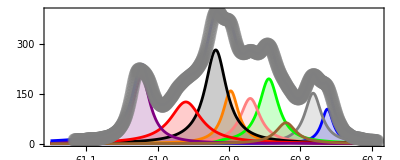

```mathematica
fit5=NonlinearModelFit[MB24h[[start;;end,1;;2]],{Lorentzian[scale1,x,ppmavg1,width1]+Lorentzian[scale2,x,ppmavg2,width2]+Lorentzian[scale3,x,ppmavg3,width3]+Lorentzian[scale4,x,ppmavg4,width4]+Lorentzian[scale5,x,ppmavg5,width5]+Lorentzian[scale6,x,ppmavg6,width6]+Lorentzian[scale7,x,ppmavg7,width7]+Lorentzian[scale8,x,ppmavg8,width8]+Lorentzian[scale2a,x,ppmavg2a,width2a]},{{scale1,30.},{scale2,30.},{scale3,30.},{scale4,10.},{scale5,50.},{scale6,10},{scale7,25.},{scale8,16.},{scale2a,10},{ppmavg1,60.7587},{ppmavg2,60.7843},{ppmavg3,60.8474},{ppmavg4,60.87},{ppmavg5,60.8985},{ppmavg6,60.9198},{ppmavg7,60.9612},{ppmavg8,61.0303},{ppmavg2a,60.81},{width1,0.02},{width2,0.01},{width3,0.01},{width4,0.01},{width5,0.02},{width6,0.02},{width7,0.015},{width8,0.01},{width2a,0.01}},x]
fit5["BestFitParameters"]
fit5["RSquared"]
fit5["ParameterTable"]
fit5["ANOVATable"]
individualMB24h=Plot[{Lorentzian[fit5["BestFitParameters"][[1]][[2]],ppm,fit5["BestFitParameters"][[10]][[2]],fit5["BestFitParameters"][[19]][[2]]],Lorentzian[fit5["BestFitParameters"][[2]][[2]],ppm,fit5["BestFitParameters"][[11]][[2]],fit5["BestFitParameters"][[20]][[2]]],Lorentzian[fit5["BestFitParameters"][[3]][[2]],ppm,fit5["BestFitParameters"][[12]][[2]],fit5["BestFitParameters"][[21]][[2]]],Lorentzian[fit5["BestFitParameters"][[4]][[2]],ppm,fit5["BestFitParameters"][[13]][[2]],fit5["BestFitParameters"][[22]][[2]]],Lorentzian[fit5["BestFitParameters"][[5]][[2]],ppm,fit5["BestFitParameters"][[14]][[2]],fit5["BestFitParameters"][[23]][[2]]],Lorentzian[fit5["BestFitParameters"][[6]][[2]],ppm,fit5["BestFitParameters"][[15]][[2]],fit5["BestFitParameters"][[24]][[2]]],Lorentzian[fit5["BestFitParameters"][[7]][[2]],ppm,fit5["BestFitParameters"][[16]][[2]],fit5["BestFitParameters"][[25]][[2]]],Lorentzian[fit5["BestFitParameters"][[8]][[2]],ppm,fit5["BestFitParameters"][[17]][[2]],fit5["BestFitParameters"][[26]][[2]]],Lorentzian[fit5["BestFitParameters"][[9]][[2]],ppm,fit5["BestFitParameters"][[18]][[2]],fit5["BestFitParameters"][[27]][[2]]]},{ppm,60.7,61.15},PlotRange->{{60.7,61.101},{0,700.}},Filling->Axis,ScalingFunctions->{"Reverse",None},Axes->{True,False},PlotStyle->{Blue,Gray,Green,Pink,Orange,Black,Red,Purple,Brown}];
cumulativeMB24h=Plot[Lorentzian[fit5["BestFitParameters"][[1]][[2]],ppm,fit5["BestFitParameters"][[10]][[2]],fit5["BestFitParameters"][[19]][[2]]]+Lorentzian[fit5["BestFitParameters"][[2]][[2]],ppm,fit5["BestFitParameters"][[11]][[2]],fit5["BestFitParameters"][[20]][[2]]]+Lorentzian[fit5["BestFitParameters"][[3]][[2]],ppm,fit5["BestFitParameters"][[12]][[2]],fit5["BestFitParameters"][[21]][[2]]]+Lorentzian[fit5["BestFitParameters"][[4]][[2]],ppm,fit5["BestFitParameters"][[13]][[2]],fit5["BestFitParameters"][[22]][[2]]]+Lorentzian[fit5["BestFitParameters"][[5]][[2]],ppm,fit5["BestFitParameters"][[14]][[2]],fit5["BestFitParameters"][[23]][[2]]]+Lorentzian[fit5["BestFitParameters"][[6]][[2]],ppm,fit5["BestFitParameters"][[15]][[2]],fit5["BestFitParameters"][[24]][[2]]]+Lorentzian[fit5["BestFitParameters"][[7]][[2]],ppm,fit5["BestFitParameters"][[16]][[2]],fit5["BestFitParameters"][[25]][[2]]]+Lorentzian[fit5["BestFitParameters"][[8]][[2]],ppm,fit5["BestFitParameters"][[17]][[2]],fit5["BestFitParameters"][[26]][[2]]]+Lorentzian[fit5["BestFitParameters"][[9]][[2]],ppm,fit5["BestFitParameters"][[18]][[2]],fit5["BestFitParameters"][[27]][[2]]],{ppm,60.7,61.15},PlotRange->{{60.7,61.1},{0,700.}},PlotStyle->{Blue},ScalingFunctions->{"Reverse",None},Axes->{True,False}];
Show[{individualMB24h,cumulativeMB24h,ListPlot[MB24h[[start;;end,1;;2]],PlotRange->{{60.5,61.1},{0,500.}},Axes->{True,False},AspectRatio->1.2,PlotStyle->{Gray,PointSize[0.025],Opacity[0.5]},ScalingFunctions->{"Reverse",None}]}]
```

FittedModel[…]

{scale1→2.98816,scale2→5.97787,scale3→9.06405,scale4→7.28528,scale5→6.21385,scale6→15.1282,scale7→10.5036,scale8→8.64467,scale2a→3.95026,ppmavg1→60.7656,ppmavg2→60.7849,ppmavg3→60.8477,ppmavg4→60.8738,ppmavg5→60.9007,ppmavg6→60.9225,ppmavg7→60.9638,ppmavg8→61.0256,ppmavg2a→60.8227,width1→0.0195017,width2→0.0285388,width3→0.0334582,width4→0.0339151,width5→0.0283504,width6→0.0399169,width7→0.053948,width8→0.0305118,width2a→0.0352354}

0.998777

General::munfl: Exp[-3871.19] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3810.59] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3736.04] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
scale1 | 2.98816 | 0.424452 | 7.04004 | 7.34348×10^-12
scale2 | 5.97787 | 0.762265 | 7.84224 | 3.3222×10^-14
scale3 | 9.06405 | 2.23957 | 4.04722 | 0.0000611396
scale4 | 7.28528 | 1.96275 | 3.71177 | 0.000231969
scale5 | 6.21385 | 1.95572 | 3.17726 | 0.00159049
scale6 | 15.1282 | 2.17151 | 6.96668 | 1.17692×10^-11
scale7 | 10.5036 | 0.978372 | 10.7358 | 4.64111×10^-24
scale8 | 8.64467 | 0.18807 | 45.9653 | 6.749×10^-171
scale2a | 3.95026 | 1.45666 | 2.71187 | 0.00695023
ppmavg1 | 60.7656 | 0.000474893 | 127956. | 0.
ppmavg2 | 60.7849 | 0.000544521 | 111630. | 0.
ppmavg3 | 60.8477 | 0.00064473 | 94377. | 0.
ppmavg4 | 60.8738 | 0.000799676 | 76123.1 | 0.
ppmavg5 | 60.9007 | 0.000696346 | 87457.5 | 0.
ppmavg6 | 60.9225 | 0.000841454 | 72401.5 | 0.
ppmavg7 | 60.9638 | 0.000965468 | 63144.2 | 0.
ppmavg8 | 61.0256 | 0.000173429 | 351876. | 0.
ppmavg2a | 60.8227 | 0.00180443 | 33707.4 | 0.
width1 | 0.0195017 | 0.00156282 | 12.4786 | 7.64452×10^-31
width2 | 0.0285388 | 0.00248482 | 11.4853 | 6.53034×10^-27
width3 | 0.0334582 | 0.0044427 | 7.53105 | 2.83917×10^-13
width4 | 0.0339151 | 0.00519767 | 6.52506 | 1.85717×10^-10
width5 | 0.0283504 | 0.00435521 | 6.50953 | 2.04116×10^-10
width6 | 0.0399169 | 0.00299014 | 13.3495 | 2.05226×10^-34
width7 | 0.053948 | 0.00301356 | 17.9017 | 2.38899×10^-54
width8 | 0.0305118 | 0.000640171 | 47.6619 | 1.03628×10^-176
width2a | 0.0352354 | 0.00691644 | 5.09444 | 5.18208×10^-7

| DF | SS | MS
Model | 27 | 1.60451×10^7 | 594264.
Error | 444 | 19646.1 | 44.2479
Uncorrected Total | 471 | 1.60648×10^7 | 
Corrected Total | 470 | 5.17227×10^6 |

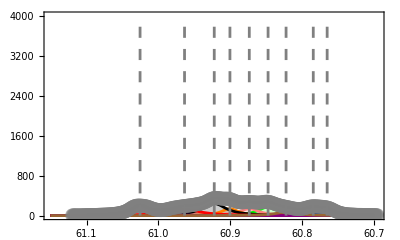

```mathematica
fit6=NonlinearModelFit[MB48h[[start;;end,1;;2]],{Lorentzian[scale1,x,ppmavg1,width1]+Lorentzian[scale2,x,ppmavg2,width2]+Lorentzian[scale3,x,ppmavg3,width3]+Lorentzian[scale4,x,ppmavg4,width4]+Lorentzian[scale5,x,ppmavg5,width5]+Lorentzian[scale6,x,ppmavg6,width6]+Lorentzian[scale7,x,ppmavg7,width7]+Lorentzian[scale8,x,ppmavg8,width8]+Lorentzian[scale2a,x,ppmavg2a,width2a]},{{scale1,2},{scale2,5},{scale3,7},{scale4, 7},{scale5,16},{scale6,12.3},{scale7,19},{scale8,7.3},{scale2a,1},{ppmavg1,60.7587},{ppmavg2,60.76},{ppmavg3,60.8474},{ppmavg4,60.87},{ppmavg5,60.8985},{ppmavg6,60.93},{ppmavg7,60.9612},{ppmavg8,61.0303},{ppmavg2a,60.81},{width1,0.02},{width2,0.03},{width3,0.06},{width4,0.04},{width5,0.04},{width6,0.04},{width7,0.05},{width8,0.03},{width2a,0.01}},x]
fit6["BestFitParameters"]
fit6["RSquared"]
fit6["ParameterTable"]
fit6["ANOVATable"]
individualMB48h=Plot[{Lorentzian[fit6["BestFitParameters"][[1]][[2]],ppm,fit6["BestFitParameters"][[10]][[2]],fit6["BestFitParameters"][[19]][[2]]],Lorentzian[fit6["BestFitParameters"][[2]][[2]],ppm,fit6["BestFitParameters"][[11]][[2]],fit6["BestFitParameters"][[20]][[2]]],Lorentzian[fit6["BestFitParameters"][[3]][[2]],ppm,fit6["BestFitParameters"][[12]][[2]],fit6["BestFitParameters"][[21]][[2]]],Lorentzian[fit6["BestFitParameters"][[4]][[2]],ppm,fit6["BestFitParameters"][[13]][[2]],fit6["BestFitParameters"][[22]][[2]]],Lorentzian[fit6["BestFitParameters"][[5]][[2]],ppm,fit6["BestFitParameters"][[14]][[2]],fit6["BestFitParameters"][[23]][[2]]],Lorentzian[fit6["BestFitParameters"][[6]][[2]],ppm,fit6["BestFitParameters"][[15]][[2]],fit6["BestFitParameters"][[24]][[2]]],Lorentzian[fit6["BestFitParameters"][[7]][[2]],ppm,fit6["BestFitParameters"][[16]][[2]],fit6["BestFitParameters"][[25]][[2]]],Lorentzian[fit6["BestFitParameters"][[8]][[2]],ppm,fit6["BestFitParameters"][[17]][[2]],fit6["BestFitParameters"][[26]][[2]]],Lorentzian[fit6["BestFitParameters"][[9]][[2]],ppm,fit6["BestFitParameters"][[18]][[2]],fit6["BestFitParameters"][[27]][[2]]]},{ppm,60.7,61.15},PlotRange->{{60.7,61.101},{0,600.}},Filling->Axis,ScalingFunctions->{"Reverse",None},Axes->{True,False},PlotStyle->{Blue,Gray,Green,Pink,Orange,Black,Red,Purple,Brown},AspectRatio->0.6];
cumulativeMB48h=Plot[Lorentzian[fit6["BestFitParameters"][[1]][[2]],ppm,fit6["BestFitParameters"][[10]][[2]],fit6["BestFitParameters"][[19]][[2]]]+Lorentzian[fit6["BestFitParameters"][[2]][[2]],ppm,fit6["BestFitParameters"][[11]][[2]],fit6["BestFitParameters"][[20]][[2]]]+Lorentzian[fit6["BestFitParameters"][[3]][[2]],ppm,fit6["BestFitParameters"][[12]][[2]],fit6["BestFitParameters"][[21]][[2]]]+Lorentzian[fit6["BestFitParameters"][[4]][[2]],ppm,fit6["BestFitParameters"][[13]][[2]],fit6["BestFitParameters"][[22]][[2]]]+Lorentzian[fit6["BestFitParameters"][[5]][[2]],ppm,fit6["BestFitParameters"][[14]][[2]],fit6["BestFitParameters"][[23]][[2]]]+Lorentzian[fit6["BestFitParameters"][[6]][[2]],ppm,fit6["BestFitParameters"][[15]][[2]],fit6["BestFitParameters"][[24]][[2]]]+Lorentzian[fit6["BestFitParameters"][[7]][[2]],ppm,fit6["BestFitParameters"][[16]][[2]],fit6["BestFitParameters"][[25]][[2]]]+Lorentzian[fit6["BestFitParameters"][[8]][[2]],ppm,fit6["BestFitParameters"][[17]][[2]],fit6["BestFitParameters"][[26]][[2]]]+Lorentzian[fit6["BestFitParameters"][[9]][[2]],ppm,fit6["BestFitParameters"][[18]][[2]],fit6["BestFitParameters"][[27]][[2]]],{ppm,60.7,61.1},PlotRange->{{60.7,61.1},{0,400.}},PlotStyle->{Black},ScalingFunctions->{"Reverse",None},Axes->{True,False}];
Show[{individualMB48h,cumulativeMB48h,dashed,ListPlot[MB48h[[start;;end,1;;2]],PlotRange->{{60.5,61.1},{0,500.}},Axes->{True,False},PlotStyle->{Gray,PointSize[0.025],Opacity[0.5]},ScalingFunctions->{"Reverse",None}]}]
```

```mathematica
(*Calculate areas of peaks*)
Areas[scale_,width_]:=scale Sqrt[1/(width^2)]
```

```mathematica
allMBp5=Sum[Areas[fit1["BestFitParameters"][[ii]][[2]],fit1["BestFitParameters"][[ii+14]][[2]]],{ii,1,7}];
MBp5peak1=Areas[fit1["BestFitParameters"][[1]][[2]],fit1["BestFitParameters"][[15]][[2]]]/allMBp5
MBp5peak2=Areas[fit1["BestFitParameters"][[2]][[2]],fit1["BestFitParameters"][[16]][[2]]]/allMBp5
MBp5peak3=Areas[fit1["BestFitParameters"][[3]][[2]],fit1["BestFitParameters"][[17]][[2]]]/allMBp5
MBp5peak5=Areas[fit1["BestFitParameters"][[4]][[2]],fit1["BestFitParameters"][[18]][[2]]]/allMBp5
MBp5peak6=Areas[fit1["BestFitParameters"][[5]][[2]],fit1["BestFitParameters"][[19]][[2]]]/allMBp5
MBp5peak7=Areas[fit1["BestFitParameters"][[6]][[2]],fit1["BestFitParameters"][[20]][[2]]]/allMBp5
MBp5peak8=Areas[fit1["BestFitParameters"][[7]][[2]],fit1["BestFitParameters"][[21]][[2]]]/allMBp5
```

0.0952726

0.124296

0.127539

0.111239

0.346653

0.064939

0.130062

```mathematica
allMB1=Sum[Areas[fit2["BestFitParameters"][[ii]][[2]],fit2["BestFitParameters"][[ii+14]][[2]]],{ii,1,7}];
MB1peak1=Areas[fit2["BestFitParameters"][[1]][[2]],fit2["BestFitParameters"][[15]][[2]]]/allMB1
MB1peak2=Areas[fit2["BestFitParameters"][[2]][[2]],fit2["BestFitParameters"][[16]][[2]]]/allMB1
MB1peak3=Areas[fit2["BestFitParameters"][[3]][[2]],fit2["BestFitParameters"][[17]][[2]]]/allMB1
MB1peak5=Areas[fit2["BestFitParameters"][[4]][[2]],fit2["BestFitParameters"][[18]][[2]]]/allMB1
MB1peak6=Areas[fit2["BestFitParameters"][[5]][[2]],fit2["BestFitParameters"][[19]][[2]]]/allMB1
MB1peak7=Areas[fit2["BestFitParameters"][[6]][[2]],fit2["BestFitParameters"][[20]][[2]]]/allMB1
MB1peak8=Areas[fit2["BestFitParameters"][[7]][[2]],fit2["BestFitParameters"][[21]][[2]]]/allMB1
```

0.104321

0.124033

0.132683

0.116956

0.319476

0.0716547

0.130876

```mathematica
allMB6=Sum[Areas[fit4["BestFitParameters"][[ii]][[2]],fit4["BestFitParameters"][[ii+15]][[2]]],{ii,1,8}];
MB6peak1=Areas[fit4["BestFitParameters"][[1]][[2]],fit4["BestFitParameters"][[17]][[2]]]/allMB6
MB6peak2=Areas[fit4["BestFitParameters"][[2]][[2]],fit4["BestFitParameters"][[18]][[2]]]/allMB6
MB6peak3=Areas[fit4["BestFitParameters"][[3]][[2]],fit4["BestFitParameters"][[19]][[2]]]/allMB6
MB6peak4=Areas[fit4["BestFitParameters"][[4]][[2]],fit4["BestFitParameters"][[20]][[2]]]/allMB6
MB6peak5=Areas[fit4["BestFitParameters"][[5]][[2]],fit4["BestFitParameters"][[21]][[2]]]/allMB6
MB6peak6=Areas[fit4["BestFitParameters"][[6]][[2]],fit4["BestFitParameters"][[22]][[2]]]/allMB6
MB6peak7=Areas[fit4["BestFitParameters"][[7]][[2]],fit4["BestFitParameters"][[23]][[2]]]/allMB6
MB6peak8=Areas[fit4["BestFitParameters"][[8]][[2]],fit4["BestFitParameters"][[24]][[2]]]/allMB6
```

0.0784444

0.111124

0.16257

0.0392071

0.132611

0.268936

0.0635984

0.149709

```mathematica
allMB24=Sum[Areas[fit5["BestFitParameters"][[ii]][[2]],fit5["BestFitParameters"][[ii+18]][[2]]],{ii,1,9}];
MB24peak1=Areas[fit5["BestFitParameters"][[1]][[2]],fit5["BestFitParameters"][[19]][[2]]]/allMB24
MB24peak2=Areas[fit5["BestFitParameters"][[2]][[2]],fit5["BestFitParameters"][[20]][[2]]]/allMB24
MB24peak3=Areas[fit5["BestFitParameters"][[3]][[2]],fit5["BestFitParameters"][[21]][[2]]]/allMB24
MB24peak4=Areas[fit5["BestFitParameters"][[4]][[2]],fit5["BestFitParameters"][[22]][[2]]]/allMB24
MB24peak5=Areas[fit5["BestFitParameters"][[5]][[2]],fit5["BestFitParameters"][[23]][[2]]]/allMB24
MB24peak6=Areas[fit5["BestFitParameters"][[6]][[2]],fit5["BestFitParameters"][[24]][[2]]]/allMB24
MB24peak7=Areas[fit5["BestFitParameters"][[7]][[2]],fit5["BestFitParameters"][[25]][[2]]]/allMB24
MB24peak8=Areas[fit5["BestFitParameters"][[8]][[2]],fit5["BestFitParameters"][[26]][[2]]]/allMB24
MB24peak2a=Areas[fit5["BestFitParameters"][[9]][[2]],fit5["BestFitParameters"][[27]][[2]]]/allMB24
```

0.0732929

0.106937

0.137298

0.0958501

0.11179

0.198392

0.0883976

0.143644

0.0443981

```mathematica
allMB48=Sum[Areas[fit6["BestFitParameters"][[ii]][[2]],fit6["BestFitParameters"][[ii+18]][[2]]],{ii,1,9}];
MB48peak1=Areas[fit6["BestFitParameters"][[1]][[2]],fit6["BestFitParameters"][[19]][[2]]]/allMB48
MB48peak2=Areas[fit6["BestFitParameters"][[2]][[2]],fit6["BestFitParameters"][[20]][[2]]]/allMB48
MB48peak3=Areas[fit6["BestFitParameters"][[3]][[2]],fit6["BestFitParameters"][[21]][[2]]]/allMB48
MB48peak4=Areas[fit6["BestFitParameters"][[4]][[2]],fit6["BestFitParameters"][[22]][[2]]]/allMB48
MB48peak5=Areas[fit6["BestFitParameters"][[5]][[2]],fit6["BestFitParameters"][[23]][[2]]]/allMB48
MB48peak6=Areas[fit6["BestFitParameters"][[6]][[2]],fit6["BestFitParameters"][[24]][[2]]]/allMB48
MB48peak7=Areas[fit6["BestFitParameters"][[7]][[2]],fit6["BestFitParameters"][[25]][[2]]]/allMB48
MB48peak8=Areas[fit6["BestFitParameters"][[8]][[2]],fit6["BestFitParameters"][[26]][[2]]]/allMB48
MB48peak2a=Areas[fit6["BestFitParameters"][[9]][[2]],fit6["BestFitParameters"][[27]][[2]]]/allMB48
```

0.0752318

0.102845

0.133012

0.105469

0.107615

0.186081

0.0955944

0.139108

0.055045

```mathematica
peak1={{30./60.,MBp5peak1},{1.,MB1peak1},{6.,MB6peak1},{24.,MB24peak1},{48.,MB48peak1}};
peak2={{30./60.,MBp5peak2},{1.,MB1peak2},{6.,MB6peak2},{24.,MB24peak2},{48.,MB48peak2}};
peak3={{30./60.,MBp5peak3},{1.,MB1peak3},{6.,MB6peak3},{24.,MB24peak3},{48.,MB48peak3}};
peak4={{0.5,0},{1,0},{6.,MB6peak4},{24.,MB24peak4},{48.,MB48peak4}};
peak5={{30./60.,MBp5peak5},{1.,MB1peak5},{6.,MB6peak5},{24.,MB24peak5},{48.,MB48peak5}};
peak6={{30./60.,MBp5peak6},{1.,MB1peak6},{6.,MB6peak6},{24.,MB24peak6},{48.,MB48peak6}};
peak7={{30./60.,MBp5peak7},{1.,MB1peak7},{6.,MB6peak7},{24.,MB24peak7},{48.,MB48peak7}};
peak8={{30./60.,MBp5peak8},{1.,MB1peak8},{6.,MB6peak8},{24.,MB24peak8},{48.,MB48peak8}};
peak2a={{0.5,0},{1,0},{6.,0},{24,MB24peak2a},{48,MB48peak2a}};
```

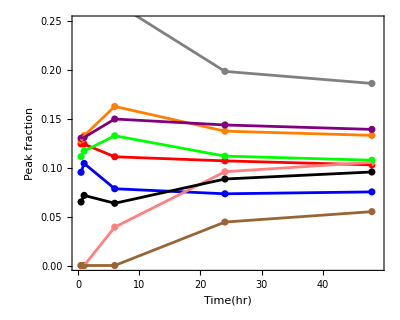

```mathematica
SetOptions[ListPlot, Frame->{{True,False},{True,False}},FrameTicks->{{LinTicks,None},{LinTicks,None}}, FrameStyle->Black, AspectRatio->0.8, LabelStyle->Directive[FontSize->12, FontFamily->"Arial"]];
SetOptions[Plot, Frame->{{True,False},{True,False}}, FrameTicks->{{LinTicks,None},{LinTicks,None}},FrameStyle->Black, AspectRatio->0.8, LabelStyle->Directive[FontSize->12, FontFamily->"Arial"]];

points=ListPlot[{peak1,peak2,peak3,peak4,peak5,peak6,peak7,peak8,peak2a}, FrameLabel->{{"Peak fraction",None},{
"Time(hr)",None}}, PlotRange->{{0,49},{0.,0.25}},PlotStyle->{Blue,Red,Orange,Pink,Green,Gray,Black,Purple,Brown},AspectRatio->0.8]; lines=ListPlot[{peak1,peak2,peak3,peak4,peak5,peak6,peak7,peak8,peak2a},Joined->True,PlotStyle->{Blue,Red,Orange,Pink,Green,Gray,Black,Purple,Brown}, PlotRange->{{0,50},{0.,0.3}}]; Show[{points,lines}]
```

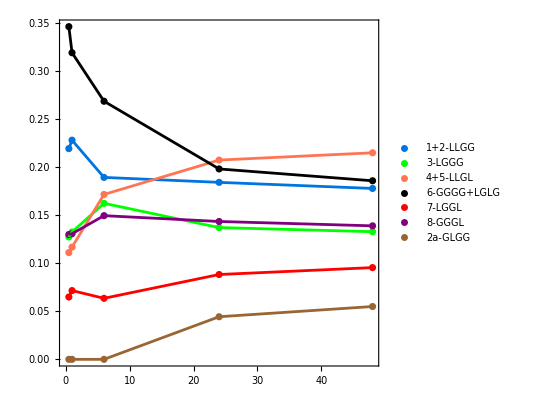

```mathematica
peak1p2={{30./60.,MBp5peak1+MBp5peak2},{1.,MB1peak1+MB1peak2},{6.,MB6peak1+MB6peak2},{24.,MB24peak1+MB6peak2},{48.,MB48peak1+MB48peak2}};
peak4p5={{30./60.,MBp5peak5},{1.,MB1peak5},{6.,MB6peak5+MB6peak4},{24.,MB24peak5+MB24peak4},{48.,MB48peak5+MB48peak5}};

points2=ListPlot[{peak1p2,peak3,peak4p5,peak6,peak7,peak8,peak2a},PlotLegends->{"1+2-LLGG","3-LGGG","4+5-LLGL","6-GGGG+LGLG","7-LGGL","8-GGGL","2a-GLGG"},PlotStyle->{RGBColor[0,0.46,0.88],Green,RGBColor[1,0.46,0.33],Black,Red,Purple,Brown},Frame->{{True,False},{True,False}}, FrameTicks->{{LinTicks,None},{LinTicks,None}},FrameStyle->Black, AspectRatio->1, LabelStyle->Directive[FontSize->12, FontFamily->"Arial",PlotRange->{{0,50},{0.,0.3501}}]]; lines2=ListPlot[{peak1p2,peak3,peak4p5,peak6,peak7,peak8,peak2a},Joined->True,PlotStyle->{RGBColor[0,0.46,0.88],Green,RGBColor[1,0.46,0.33],Black,Red,Purple,Brown}]; 
Show[{points2,lines2}]
(*Export["output.csv",peak1p2]*)
```

```mathematica
(*The excel file referenced here and stochastic model data used to populate the excel spreadsheet are publicly posted at https://doi.org/10.18738/T8/QYLE8E. The stochastic model data file that these values are calculated from is called PLGA6040_008kT.seq*)
Stopeak1 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",2,21;;37,{1,3}}];
Stopeak2 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",2,21;;37,{1,4}}];
Stopeak3 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",2,21;;37,{1,5}}];
Stopeak4 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",2,21;;37,{1,6}}];
Stopeak5 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",2,21;;37,{1,7}}];
Stopeak6 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",2,21;;37,{1,8}}];
Stopeak7 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",2,21;;37,{1,9}}];
Stopeak8 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",2,21;;37,{1,10}}];
Stopeak1p7 = Import["C:\\Users\\lkueh\\Box\\Lynd Group\\Louise\\Paper outlines\\Blockiness definition\\PLGA_modelseq_05032024.xlsx",{"Data",2,21;;37,{1,23}}];

SetOptions[ListPlot, Frame->{{True,False},{True,False}},FrameTicks->{{LinTicks,None},{LinTicks,None}}, FrameStyle->Black, AspectRatio->0.8, LabelStyle->Directive[FontSize->12, FontFamily->"Arial"]];
SetOptions[Plot, Frame->{{True,False},{True,False}}, FrameTicks->{{LinTicks,None},{LinTicks,None}},FrameStyle->Black, AspectRatio->1, LabelStyle->Directive[FontSize->12, FontFamily->"Arial"]];
```

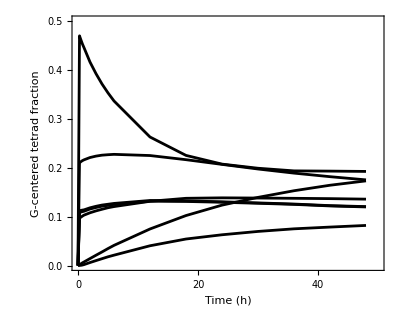

```mathematica
stolines = ListPlot[{Stopeak1p7,Stopeak2,Stopeak3,Stopeak4,Stopeak5,Stopeak6,Stopeak8},Joined->True,PlotStyle->Black,FrameLabel->{{"G-centered tetrad fraction",None},{"Time (h)",None}},PlotRange->{{0,50},{0.,0.501}},AspectRatio->0.8]
(*PlotStyle->{Black,Purple,Brown,RGBColor[0,0.46,0.88],Directive[Green,Dashed],Red,RGBColor[1,0.46,0.33]}*)
```